# Eu_5 In_2 Sb_6 Dipolar Energy

## General

```mathematica
Clear["Global`*"]

(*Lattice parameters. Define the atomic positions for each Eu site. Eu1 and Eu3 are 4g. Eu2 is 2a.*)
a = 12.510;
b = 14.584;
c = 4.6243;
wy4g[x_,y_]:={Mod[{x,y,0},1], Mod[{x+1/2,-y+1/2,0},1], Mod[{-x+1/2,y+1/2,0},1], Mod[{-x,-y,0},1]};
wy2a={{0,0,0},{1/2,1/2,0}};
x1=0.32749;
x3=0.9128;
y1=0.01894;
y3=0.7505;

(*Propagation vectors. Define the atomic moments for each Eu site. Eu1 and Eu3 are 4g. Eu2 is 2a. Assuming irrep 3 for now.*)
k1 = {0,0,0}*{2π/a, 2π/b, 2π/c};
k2 = {0,0,1/2}*{2π/a, 2π/b, 2π/c};
wy4gBas1 = {{1,0,0},{1,0,0},{1,0,0},{1,0,0}};
wy4gBas2 = {{0,1,0},{0,-1,0},{0,-1,0},{0,1,0}};
wy2aBas1 = {{1,0,0},{1,0,0}};
wy2aBas2 = {{0,1,0},{0,-1,0}};
m4g[a_, b_] := a wy4gBas1 + b wy4gBas2;
m2a[a_, b_] := a wy2aBas1 + b wy2aBas2;

(*Atomic positions and spins in the unit cell. Should automate adjusting unit cell positions and moments for each k-vectors and make this so it doesn't only work for my particular structure.*)
rUC[ph_] := Module[{tmp}, If[ph==1, tmp=Flatten[{wy4g[x1, y1], wy2a, wy4g[x3, y3]}, 1]]; If[ph==2, tmp=Flatten[{wy4g[x1, y1], wy2a, wy4g[x3, y3], wy4g[x1, y1]+Table[{0,0,1}, Length[wy4g[x1, y1]]], wy2a+Table[{0,0,1}, Length[wy2a]], wy4g[x3, y3]+Table[{0,0,1}, Length[wy4g[x3, y3]]]}, 1]]; tmp];
mUC[mix_, ph_] := Module[{tmp}, If[ph==1, tmp=Flatten[{m4g[mix[[1]], mix[[2]]], m2a[mix[[3]], mix[[4]]], m4g[mix[[5]], mix[[6]]]}, 1]]; If[ph==2, tmp=Flatten[{m4g[mix[[1]], mix[[2]]], m2a[mix[[3]], mix[[4]]], m4g[mix[[5]], mix[[6]]], m4g[-mix[[1]], mix[[2]]], m2a[-mix[[3]], mix[[4]]], m4g[-mix[[5]], mix[[6]]]}, 1]]; tmp]; (*ma1, mb1, ma2, mb2, ma3, mb3*)

(*Loop through source charges and act on each test charge in the zeroth cell adding energy. Get energy per unit cell then divide by the number of Eu atoms in a unit cell to get meV/Eu. Prevent double-counting in the 0th unit cell. Convert to meV.*)
Subscript[μ, 0] = 1.25663706*10^(-6);
hat[v_] := v/Norm[v];
conv = (10^30)*(9.274*10^-24)^2*(6.242*10^21); (*Convert to meV. Ang to m and muB to J/T then SI to meV.*)
pos[pos0_, ni_, nj_, nk_, ph_]:={a (pos0[[1]] + ni), b (pos0[[2]] + nj), c (pos0[[3]] + ph*nk)}; (*Make general for all phases.*)
U[mix_, kVec_, dMax_, ph_]:=Module[{nMax, rS, rZero, mS, rT, mT, sep, u, tmp}, u=0; nMax=Ceiling[dMax/(ph*c)]; Do[Do[Do[Do[rS=pos[rUC[ph][[lS]], ni, nj, nk, ph]; rZero=pos[rUC[ph][[lS]], 0, 0, 0, ph]; If[Norm[rS-rZero]<dMax, mS=0; Do[mS=mS+mUC[mix[[k,All]], ph][[lS]]*ⅇ^(ⅈ*(rS-rZero).kVec[[k]]), {k, Length[kVec]}]; Do[rT= pos[rUC[ph][[lT]], 0, 0, 0, ph]; If[rT!=rS, mT=0; Do[mT=mT+mUC[mix[[k,All]], ph][[lT]], {k, Length[kVec]}]; sep=rT-rS; u=u-mT.(Subscript[μ, 0]/(4 π)*(3 *(mS.hat[sep])hat[sep]- mS)/Norm[sep]^3)*If[rS-rZero=={0.,0.,0.}, 1/2, 1]], {lT, Length[rUC[ph]]}]], {lS, Length[rUC[ph]]}], {nk,-nMax, nMax}], {nj, -nMax, nMax}], {ni, -nMax, nMax}]; Chop[u/Length[rUC[ph]]*conv]];
```

## Phase 1

```mathematica
ma1Ph1=0;
mb1Ph1=-5;
ma2Ph1=0;
mb2Ph1=7;
ma3Ph1=0;
mb3Ph1=6;

dMax=100;

U[{{ma1Ph1, mb1Ph1, ma2Ph1, mb2Ph1, ma3Ph1, mb3Ph1}}, {k1}, dMax, 1]
```

-0.0739391

## Phase 2

```mathematica
ma1Ph2k1=0;
mb1Ph2k1=-5;
ma2Ph2k1=0;
mb2Ph2k1=7;
ma3Ph2k1=0;
mb3Ph2k1=7;

ma1Ph2k2=7;
mb1Ph2k2=0;
ma2Ph2k2=0;
mb2Ph2k2=0;
ma3Ph2k2=4;
mb3Ph2k2=0;

dMax=100;

U[{{ma1Ph2k1, mb1Ph2k1, ma2Ph2k1, mb2Ph2k1, ma3Ph2k1, mb3Ph2k1}, {ma1Ph2k2, mb1Ph2k2, ma2Ph2k2, mb2Ph2k2, ma3Ph2k2, mb3Ph2k2}}, {k1, k2}, dMax, 2]
```

-0.140221

## Energy Versus d_Max: Phase 1

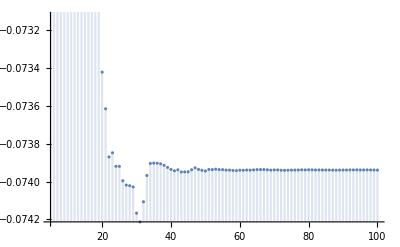

```mathematica
ma1Ph1=0;
mb1Ph1=-5;
ma2Ph1=0;
mb2Ph1=7;
ma3Ph1=0;
mb3Ph1=6;

DiscretePlot[U[{{ma1Ph1, mb1Ph1, ma2Ph1, mb2Ph1, ma3Ph1, mb3Ph1}}, {k1}, dMax, 1], {dMax, Ceiling[c], 100}]
```

## Energy Versus d_Max: Phase 2

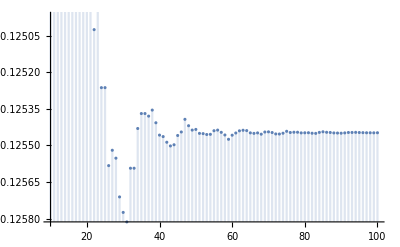

```mathematica
ma1Ph2k1=0;
mb1Ph2k1=-5;
ma2Ph2k1=0;
mb2Ph2k1=7;
ma3Ph2k1=0;
mb3Ph2k1=7;

ma1Ph2k2=6;
mb1Ph2k2=0;
ma2Ph2k2=0;
mb2Ph2k2=0;
ma3Ph2k2=4;
mb3Ph2k2=0;

DiscretePlot[U[{{ma1Ph2k1,mb1Ph2k1,ma2Ph2k1,mb2Ph2k1,ma3Ph2k1,mb3Ph2k1},{ma1Ph2k2,mb1Ph2k2,ma2Ph2k2,mb2Ph2k2,ma3Ph2k2,mb3Ph2k2}},{k1,k2}, dMax, 2], {dMax, Ceiling[2*c], 100}]
```

## Test 1: Saturated moments k=0, same ab.

```mathematica
ma1Ph1=4.95;
mb1Ph1=4.95;
ma2Ph1=4.95;
mb2Ph1=4.95;
ma3Ph1=4.95;
mb3Ph1=4.95;

dMax=100;

U[{{ma1Ph1, mb1Ph1, ma2Ph1, mb2Ph1, ma3Ph1, mb3Ph1}}, {k1}, dMax, 1]
```

0.0837763

## Test 2: Saturated moments k=0, only a.

```mathematica
ma1Ph1=7;
mb1Ph1=0;
ma2Ph1=7;
mb2Ph1=0;
ma3Ph1=7;
mb3Ph1=0;

dMax=100;

U[{{ma1Ph1, mb1Ph1, ma2Ph1, mb2Ph1, ma3Ph1, mb3Ph1}}, {k1}, dMax, 1]
```

0.0250253

## Test 3: Saturated moments k=0, only b.

```mathematica
ma1Ph1=0;
mb1Ph1=7;
ma2Ph1=0;
mb2Ph1=7;
ma3Ph1=0;
mb3Ph1=7;

dMax=100;

U[{{ma1Ph1, mb1Ph1, ma2Ph1, mb2Ph1, ma3Ph1, mb3Ph1}}, {k1}, dMax, 1]
```

0.153022

## Test 4: Saturated moments k=0, only b aligned.

```mathematica
ma1Ph1=0;
mb1Ph1=-7;
ma2Ph1=0;
mb2Ph1=7;
ma3Ph1=0;
mb3Ph1=7;

dMax=100;

U[{{ma1Ph1, mb1Ph1, ma2Ph1, mb2Ph1, ma3Ph1, mb3Ph1}}, {k1}, dMax, 1]
```

-0.0879231

## Test 5: Saturated moments multi-k, same ab

```mathematica
ma1Ph2k1=0;
mb1Ph2k1=-4.95;
ma2Ph2k1=0;
mb2Ph2k1=4.95;
ma3Ph2k1=0;
mb3Ph2k1=4.95;

ma1Ph2k2=4.95;
mb1Ph2k2=0;
ma2Ph2k2=4.95;
mb2Ph2k2=0;
ma3Ph2k2=4.95;
mb3Ph2k2=0;

dMax=100;

U[{{ma1Ph2k1, mb1Ph2k1, ma2Ph2k1, mb2Ph2k1, ma3Ph2k1, mb3Ph2k1}, {ma1Ph2k2, mb1Ph2k2, ma2Ph2k2, mb2Ph2k2, ma3Ph2k2, mb3Ph2k2}}, {k1, k2}, dMax, 2]
```

-0.100516